```mathematica
NN = 2
```

2

```mathematica
m0[a_] := ⅇ^(1/NN Log[a])

σ0[a_] := ⅇ^(1/NN Log[ 1 + a])



mj[a_,j_] := m0[a] ⅇ^(2 π ⅈ j / NN)

m1[a_] := m0[a] ⅇ^(2 π ⅈ  / NN)

σ1[a_] := σ0[a]  ⅇ^((2 π ⅈ)/NN)



W0[a_] := (- 1)/(2π)( NN σ0[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ0[a] - mj[a,j] ])



W1[a_] := -1/(2π) (NN σ1[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ1[a] - mj[a,j] ] )



Tower[a_, k_] := (( ⅇ^(2 π ⅈ / NN) - 1 ) W0[a] + ⅈ mj[a,k])/(m1[a] - m0[a])
```

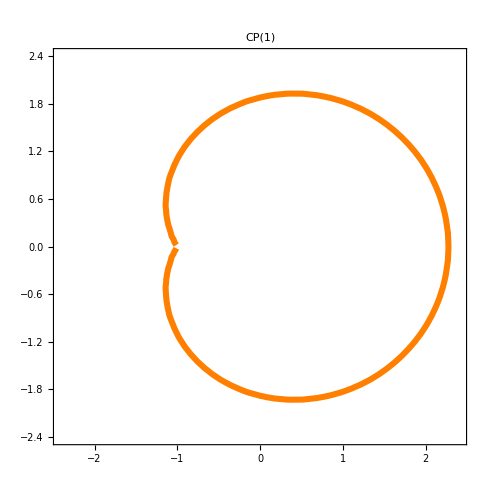

```mathematica
ContourPlot[   {  Re[ Tower[x + ⅈ y, 1] ] == 0  },
                             { x , -2.4, 2.4}, { y, -2.4, 2.4 },
                             ContourStyle->{ Directive[ Thickness[0.009], Orange ] } , 
                             PlotLabel-> Style["CP(1)",FontSize->24], LabelStyle->Directive[FontSize->18]]
```

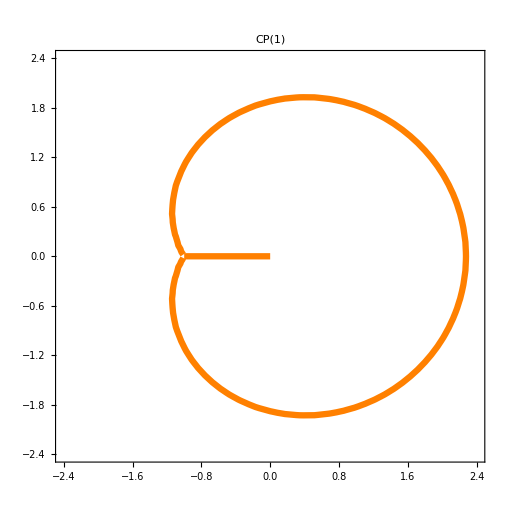

```mathematica
Show[%,ContourPlot[ y == 0, {x, -1, 0}, {y,-0.5,0.5}, ContourStyle->{ Directive[ Thickness[0.009], Orange ] } ] ]
```

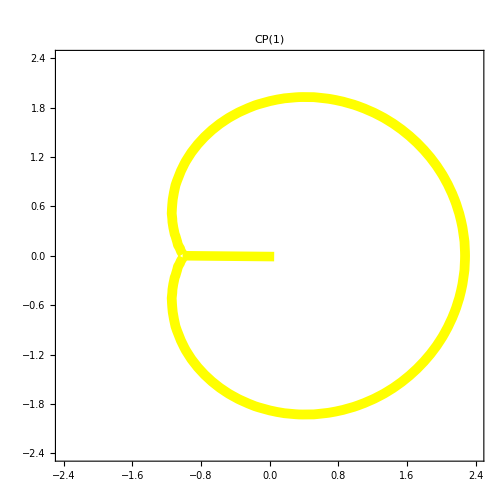

-Graphics-